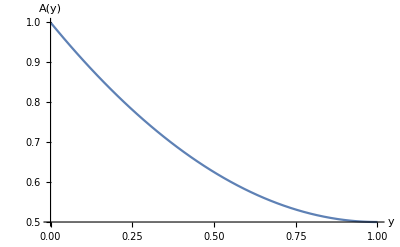

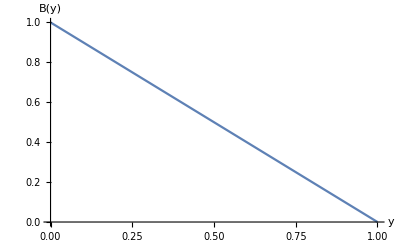

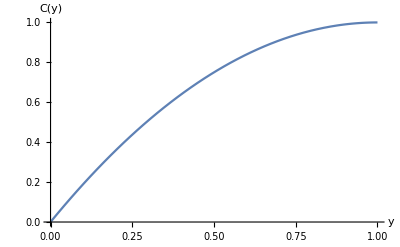

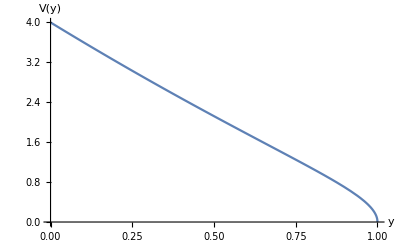

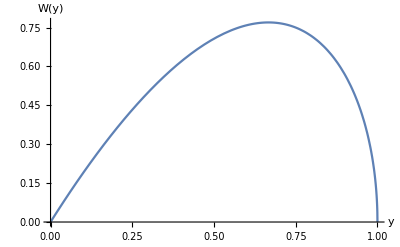

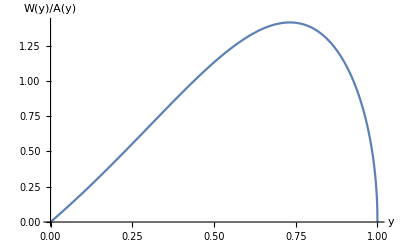

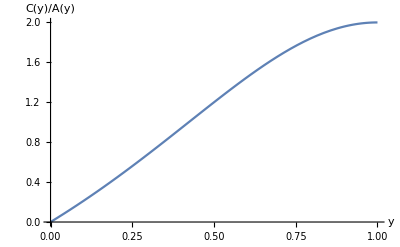

```mathematica
a[y_]=1-y+y*y/2;
b[y_]=1-y;
c[y_]=y*(2-y);
v[y_]=2*(2-y)*Sqrt[1-y];
w[y_]=2*y*Sqrt[1-y];
Plot[a[y],{y,0,1},AxesLabel->{"y","A(y)"}]
Plot[b[y],{y,0,1},AxesLabel->{"y","B(y)"}]
Plot[c[y],{y,0,1},AxesLabel->{"y","C(y)"}]
Plot[v[y],{y,0,1},AxesLabel->{"y","V(y)"}]
Plot[w[y],{y,0,1},AxesLabel->{"y","W(y)"}]
Plot[w[y]/a[y],{y,0,1},AxesLabel->{"y","W(y)/A(y)"}]
Plot[c[y]/a[y],{y,0,1},AxesLabel->{"y","C(y)/A(y)"}]
```